```mathematica
Table[Join[{master},Buddy[master,Map[ListofVars,ExpressionToList[allCrit]]],Map[Framed[#]&,AntiBuddy[master,Map[ListofVars,ExpressionToList[allCrit]]]]],{master,ZeVars8}]/.RepGraph2["C"]
```

{{-Graphics-29525045,-Graphics-36194013♁245,-Graphics-296330245,-Graphics-36086013♁45},{-Graphics-29527035},{-Graphics-29533034,-Graphics-383080134♁25,-Graphics-29560025♁34,-Graphics-382810134},{-Graphics-29551025},{-Graphics-29560025♁34,-Graphics-382810134,-Graphics-29533034,-Graphics-383080134♁25},{-Graphics-29605024},{-Graphics-29608024♁35},{-Graphics-296330245,-Graphics-36086013♁45,-Graphics-29525045,-Graphics-36194013♁245},{-Graphics-29767023,-Graphics-31984014♁235,-Graphics-297970235,-Graphics-31954014♁23},{-Graphics-297970235,-Graphics-31954014♁23,-Graphics-29767023,-Graphics-31984014♁235},{-Graphics-30253015,-Graphics-368980135♁24,-Graphics-30334015♁24,-Graphics-368170135},{-Graphics-30334015♁24,-Graphics-368170135,-Graphics-30253015,-Graphics-368980135♁24},{-Graphics-31711014},{-Graphics-31714014♁35},{-Graphics-31738014♁25},{-Graphics-31954014♁23,-Graphics-297970235,-Graphics-29767023,-Graphics-31984014♁235},{-Graphics-31984014♁235,-Graphics-29767023,-Graphics-297970235,-Graphics-31954014♁23},{-Graphics-36085013},{-Graphics-36086013♁45,-Graphics-296330245,-Graphics-29525045,-Graphics-36194013♁245},{-Graphics-36112013♁25},{-Graphics-36166013♁24},{-Graphics-36194013♁245,-Graphics-29525045,-Graphics-296330245,-Graphics-36086013♁45},{-Graphics-368170135,-Graphics-30334015♁24,-Graphics-30253015,-Graphics-368980135♁24},{-Graphics-368980135♁24,-Graphics-30253015,-Graphics-30334015♁24,-Graphics-368170135},{-Graphics-382810134,-Graphics-29560025♁34,-Graphics-29533034,-Graphics-383080134♁25},{-Graphics-383080134♁25,-Graphics-29533034,-Graphics-29560025♁34,-Graphics-382810134},{-Graphics-49207012,-Graphics-514780124♁35,-Graphics-49210012♁35,-Graphics-514750124},{-Graphics-49210012♁35,-Graphics-514750124,-Graphics-49207012,-Graphics-514780124♁35},{-Graphics-514750124,-Graphics-49210012♁35,-Graphics-49207012,-Graphics-514780124♁35},{-Graphics-514780124♁35,-Graphics-49207012,-Graphics-49210012♁35,-Graphics-514750124}}

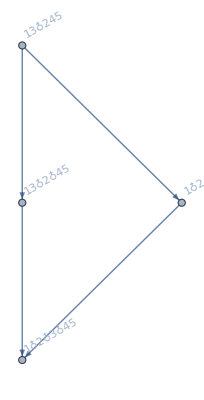
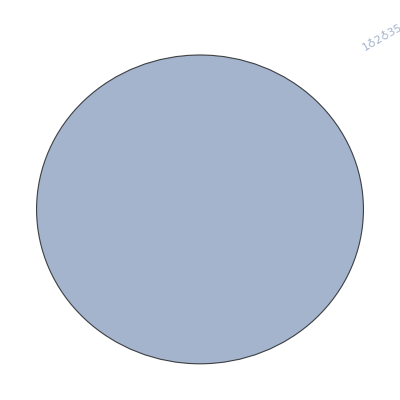
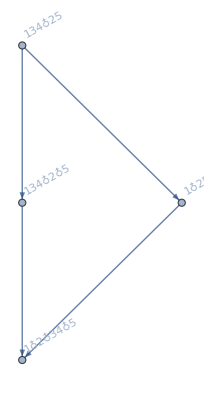
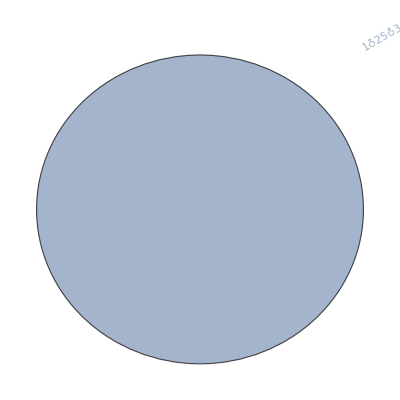
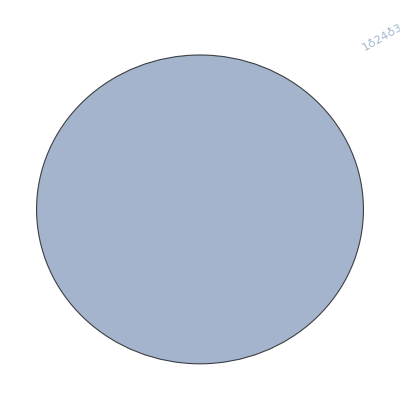
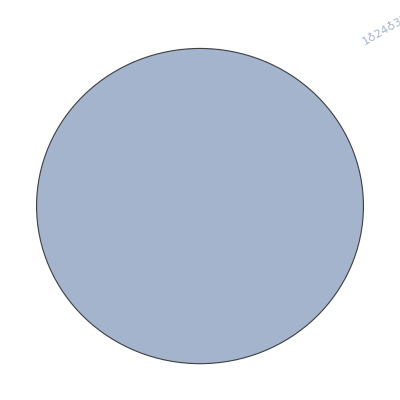
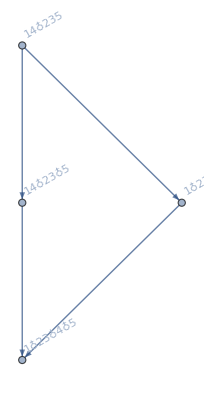
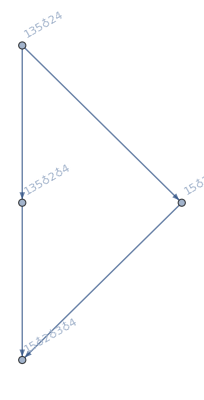
{-Graphics-{v1x2x3x45,v13x245,v1x245x3,v13x2x45},-Graphics-{v1x2x35x4},-Graphics-{v1x2x34x5,v134x25,v1x25x34,v134x2x5},-Graphics-{v1x25x3x4},-Graphics-{v1x25x34,v134x2x5,v1x2x34x5,v134x25},-Graphics-{v1x24x3x5},-Graphics-{v1x24x35},-Graphics-{v1x245x3,v13x2x45,v1x2x3x45,v13x245},-Graphics-{v1x23x4x5,v14x235,v1x235x4,v14x23x5},-Graphics-{v1x235x4,v14x23x5,v1x23x4x5,v14x235},-Graphics-{v15x2x3x4,v135x24,v15x24x3,v135x2x4},-Graphics-{v15x24x3,v135x2x4,v15x2x3x4,v135x24},-Graphics-{v14x2x3x5},-Graphics-{v14x2x35},-Graphics-{v14x25x3},-Graphics-{v14x23x5,v1x235x4,v1x23x4x5,v14x235},-Graphics-{v14x235,v1x23x4x5,v1x235x4,v14x23x5},-Graphics-{v13x2x4x5},-Graphics-{v13x2x45,v1x245x3,v1x2x3x45,v13x245},-Graphics-{v13x25x4},-Graphics-{v13x24x5},-Graphics-{v13x245,v1x2x3x45,v1x245x3,v13x2x45},-Graphics-{v135x2x4,v15x24x3,v15x2x3x4,v135x24},-Graphics-{v135x24,v15x2x3x4,v15x24x3,v135x2x4},-Graphics-{v134x2x5,v1x25x34,v1x2x34x5,v134x25},-Graphics-{v134x25,v1x2x34x5,v1x25x34,v134x2x5},-Graphics-{v12x3x4x5,v124x35,v12x35x4,v124x3x5},-Graphics-{v12x35x4,v124x3x5,v12x3x4x5,v124x35},-Graphics-{v124x3x5,v12x35x4,v12x3x4x5,v124x35},-Graphics-{v124x35,v12x3x4x5,v12x35x4,v124x3x5}}

```mathematica
Table[Labeled[FormulaGraphReverse[Join[{master},Buddy[master,Map[ListofVars,ExpressionToList[allCrit]]],AntiBuddy[master,Map[ListofVars,ExpressionToList[allCrit]]]]],Join[{master},Buddy[master,Map[ListofVars,ExpressionToList[allCrit]]],Map[Framed[#]&,AntiBuddy[master,Map[ListofVars,ExpressionToList[allCrit]]]]]],{master,ZeVars8}]
```

```mathematica
Sort[Table[FormulaGraphReverse[Join[{master},Buddy[master,Map[ListofVars,ExpressionToList[allCrit]]],AntiBuddy[master,Map[ListofVars,ExpressionToList[allCrit]]]]],{master,ZeVars8}]/.RepGraph2["C"],VertexCount[#1]<VertexCount[#2]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
not12={v1x2x3x45,v13x245,v1x245x3,v13x2x45}
```

{v1x2x3x45,v13x245,v1x245x3,v13x2x45}

```mathematica
not12/.RepGraph["C"]
```

{-Graphics-295250,-Graphics-361940,-Graphics-296330,-Graphics-360860}

```mathematica
Fold[And,Table[v==0,{v,not12}]]
```

v1x2x3x45==0&&v13x245==0&&v1x245x3==0&&v13x2x45==0

```mathematica
boega=Fold[Or,Select[ExpressionToList[allCrit],Intersection[ListofVars[#],tri]=={}&]];Length[boega]
```

32

```mathematica
Length[allCrit]
```

544

```mathematica
Fold[And,Table[v==0,{v,Take[not12,3]}]]
```

v1x2x3x45==0&&v13x245==0&&v1x245x3==0

```mathematica
Reduce[Fold[And,Table[v==0,{v,not12}]]&&boega]
```

False

```mathematica
Table[s->Reduce[Fold[And,Table[v==0,{v,s}]]&&boega],{s,Subsets[not12,{4}]}]/.RepGraph["C"]
```

{{-Graphics-295250,-Graphics-361940,-Graphics-296330,-Graphics-360860}→False}

```mathematica
Table[s->Reduce[Fold[And,Table[v==0,{v,s}]]&&boega],{s,Subsets[not12,{3}]}]/.RepGraph["C"]
```

{{-Graphics-295250,-Graphics-361940,-Graphics-296330}→False,{-Graphics-295250,-Graphics-361940,-Graphics-360860}→False,{-Graphics-295250,-Graphics-296330,-Graphics-360860}→False,{-Graphics-361940,-Graphics-296330,-Graphics-360860}→False}

```mathematica
Table[s->Reduce[Fold[And,Table[v==0,{v,s}]]&&boega],{s,Subsets[not12,{4}]}]/.RepGraph["C"]
```

{{-Graphics-295250,-Graphics-361940,-Graphics-296330,-Graphics-360860}→False}

```mathematica
Table[s->!BooleanQ[Reduce[Fold[And,Table[v==0,{v,s}]]&&boega]],{s,Subsets[not12,{2}]}]/.RepGraph["C"]
```

{{-Graphics-295250,-Graphics-361940}→True,{-Graphics-295250,-Graphics-296330}→False,{-Graphics-295250,-Graphics-360860}→False,{-Graphics-361940,-Graphics-296330}→False,{-Graphics-361940,-Graphics-360860}→False,{-Graphics-296330,-Graphics-360860}→True}

```mathematica
Table[s->!BooleanQ[Reduce[Fold[And,Table[v==0,{v,s}]]&&boega]],{s,Subsets[not12,{1}]}]/.RepGraph["C"]
```

{{-Graphics-295250}→True,{-Graphics-361940}→True,{-Graphics-296330}→True,{-Graphics-360860}→True}

```mathematica
Table[s->!BooleanQ[Reduce[Fold[And,Table[v==0,{v,s}]]&&boega]],{s,Subsets[not12,{2}]}]/.RepGraph["C"]
```

{{-Graphics-295250,-Graphics-361940}→True,{-Graphics-295250,-Graphics-296330}→False,{-Graphics-295250,-Graphics-360860}→False,{-Graphics-361940,-Graphics-296330}→False,{-Graphics-361940,-Graphics-360860}→False,{-Graphics-296330,-Graphics-360860}→True}

```mathematica
Reduce[Fold[And,Table[v==0,{v,RandomSample[not12,2]}]]&&boega]
```

(v14x2x3x5>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x3x4>0&&v135x24>0&&v1x2x34x5>0&&v134x25>0&&v1x2x35x4>0&&v12x3x4x5>0&&v1x2x3x45==0&&v124x35>0)||(v14x2x3x5>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x3x4>0&&v135x24>0&&v1x2x34x5>0&&v134x25>0&&v1x2x35x4>0&&v12x3x4x5>0&&v1x2x3x45==0&&v124x35>0)||(v14x2x3x5>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x3x4>0&&v135x2x4>0&&v1x2x34x5>0&&v134x25>0&&v1x2x35x4>0&&v12x3x4x5>0&&v1x2x3x45==0&&v124x35>0)||(v14x2x3x5>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x3x4>0&&v135x2x4>0&&v1x2x34x5>0&&v134x25>0&&v1x2x35x4>0&&v12x3x4x5>0&&v1x2x3x45==0&&v124x35>0)||(v14x2x3x5>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x34>0&&v135x24>0&&v1x25x3x4>0&&v134x2x5>0&&v1x2x35x4>0&&v12x3x4x5>0&&v1x2x3x45==0&&v124x35>0)||(v14x2x3x5>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x34>0&&v135x24>0&&v1x25x3x4>0&&v134x2x5>0&&v1x2x35x4>0&&v12x3x4x5>0&&v1x2x3x45==0&&v124x35>0)||(v14x2x3x5>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x34>0&&v135x2x4>0&&v1x25x3x4>0&&v134x2x5>0&&v1x2x35x4>0&&v12x3x4x5>0&&v1x2x3x45==0&&v124x35>0)||(v14x2x3x5>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x34>0&&v135x2x4>0&&v1x25x3x4>0&&v134x2x5>0&&v1x2x35x4>0&&v12x3x4x5>0&&v1x2x3x45==0&&v124x35>0)||(v14x2x3x5>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x3x4>0&&v135x24>0&&v1x2x34x5>0&&v134x25>0&&v1x2x35x4>0&&v12x35x4>0&&v1x2x3x45==0&&v124x3x5>0)||(v14x2x3x5>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x3x4>0&&v135x24>0&&v1x2x34x5>0&&v134x25>0&&v1x2x35x4>0&&v12x35x4>0&&v1x2x3x45==0&&v124x3x5>0)||(v14x2x3x5>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x3x4>0&&v135x2x4>0&&v1x2x34x5>0&&v134x25>0&&v1x2x35x4>0&&v12x35x4>0&&v1x2x3x45==0&&v124x3x5>0)||(v14x2x3x5>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x3x4>0&&v135x2x4>0&&v1x2x34x5>0&&v134x25>0&&v1x2x35x4>0&&v12x35x4>0&&v1x2x3x45==0&&v124x3x5>0)||(v14x2x3x5>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x34>0&&v135x24>0&&v1x25x3x4>0&&v134x2x5>0&&v1x2x35x4>0&&v12x35x4>0&&v1x2x3x45==0&&v124x3x5>0)||(v14x2x3x5>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x34>0&&v135x24>0&&v1x25x3x4>0&&v134x2x5>0&&v1x2x35x4>0&&v12x35x4>0&&v1x2x3x45==0&&v124x3x5>0)||(v14x2x3x5>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x34>0&&v135x2x4>0&&v1x25x3x4>0&&v134x2x5>0&&v1x2x35x4>0&&v12x35x4>0&&v1x2x3x45==0&&v124x3x5>0)||(v14x2x3x5>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v13x2x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x3x5>0&&v13x245==0&&v1x25x34>0&&v135x2x4>0&&v1x25x3x4>0&&v134x2x5>0&&v1x2x35x4>0&&v12x35x4>0&&v1x2x3x45==0&&v124x3x5>0)

```mathematica
Map[ListofVars,ExpressionToList[allCrit]]
```

{{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x25x3,v14x2x35,v15x2x3x4,v1x23x4x5,v1x24x35,v1x2x34x5,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x24x5,v13x25x4,v14x23x5,v14x25x3,v14x2x35,v15x2x3x4,v1x235x4,v1x24x35,v1x2x34x5,v1x2x3x45},539,{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x35,v1x25x34,v1x25x3x4},{v124x3x5,v12x35x4,v134x2x5,v135x2x4,v13x2x45,v13x2x4x5,v14x23x5,v14x2x3x5,v15x24x3,v1x235x4,v1x245x3,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x35x4}}
 |  |  |  |

```mathematica
Table[ColorData["DarkRainbow"][k/30],{k,1,30}]
```

{RGBColor[0.243041, 0.34177433333333335, 0.5694589999999999],RGBColor[0.248346, 0.34333366666666665, 0.563805],RGBColor[0.253651, 0.344893, 0.558151],RGBColor[0.25724233333333335, 0.3709366666666667, 0.5004006666666666],RGBColor[0.2608336666666667, 0.3969803333333333, 0.4426503333333333],RGBColor[0.264425, 0.423024, 0.3849],RGBColor[0.2734396666666667, 0.44107266666666667, 0.34707033333333337],RGBColor[0.2824543333333333, 0.4591213333333333, 0.3092406666666667],RGBColor[0.291469, 0.47717, 0.271411],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335],RGBColor[0.3747523333333333, 0.5292866666666667, 0.2516836666666667],RGBColor[0.416394, 0.555345, 0.24182],RGBColor[0.48588466666666663, 0.594664, 0.249312],RGBColor[0.5553753333333333, 0.633983, 0.256804],RGBColor[0.624866, 0.673302, 0.264296],RGBColor[0.6875883333333334, 0.7042986666666666, 0.27735],RGBColor[0.7503106666666667, 0.7352953333333333, 0.290404],RGBColor[0.813033, 0.766292, 0.303458],RGBColor[0.834647, 0.754543, 0.3112706666666667],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333],RGBColor[0.877875, 0.731045, 0.326896],RGBColor[0.8561856666666666, 0.6602613333333333, 0.31908366666666665],RGBColor[0.8344963333333333, 0.5894776666666667, 0.31127133333333334],RGBColor[0.812807, 0.518694, 0.303459],RGBColor[0.7851613333333333, 0.4255956666666667, 0.279293],RGBColor[0.7575156666666667, 0.33249733333333337, 0.255127],RGBColor[0.72987, 0.239399, 0.230961],RGBColor[0.72987, 0.239399, 0.230961],RGBColor[0.72987, 0.239399, 0.230961],RGBColor[0.72987, 0.239399, 0.230961]}

```mathematica
Table[Join[{master},Buddy[master,Map[ListofVars,ExpressionToList[allCrit]]]],{master,ZeVars8}]//Length
```

30

```mathematica
repColor=Block[{
sols={},
todo=ZeVars8,
i,
current,
buddy,
antibuddy,
range=Map[ListofVars,ExpressionToList[allCrit]],
qua=Table[allGraphs5[k,"colofour"],{k,quads}]
},
todo=Select[todo,!MemberQ[qua,#]&];
For[i=1,Length[todo]≠0,i++,
current=todo[[1]];
buddy=Join[{current},Buddy[current,range]];
antibuddy=Join[AntiBuddy[current,range]];
Table[AppendTo[sols,b->Style[b,ColorData["DarkRainbow"][i/5]]],{b,buddy}];
Table[AppendTo[sols,b->Style[b,Underlined,ColorData["DarkRainbow"][i/5]]],{b,antibuddy}];
todo=Select[todo,!MemberQ[buddy,#]&&!MemberQ[antibuddy,#]&];
];
sols
]
```

{v1x2x3x45→v1x2x3x45,v13x245→v13x245,v1x245x3→v1x245x3,v13x2x45→v13x2x45,v1x2x34x5→v1x2x34x5,v134x25→v134x25,v1x25x34→v1x25x34,v134x2x5→v134x2x5,v1x24x35→v1x24x35,v1x23x4x5→v1x23x4x5,v14x235→v14x235,v1x235x4→v1x235x4,v14x23x5→v14x23x5,v15x2x3x4→v15x2x3x4,v135x24→v135x24,v15x24x3→v15x24x3,v135x2x4→v135x2x4,v14x2x35→v14x2x35,v14x25x3→v14x25x3,v13x25x4→v13x25x4,v13x24x5→v13x24x5,v12x3x4x5→v12x3x4x5,v124x35→v124x35,v12x35x4→v12x35x4,v124x3x5→v124x3x5}

```mathematica
repColorValue=Block[{
sols={},
todo=ZeVars8,
i,
current,
buddy,
antibuddy,
range=Map[ListofVars,ExpressionToList[allCrit]],
qua=Table[allGraphs5[k,"colofour"],{k,quads}]
},
todo=Select[todo,!MemberQ[qua,#]&];
For[i=1,Length[todo]≠0,i++,
current=todo[[1]];
buddy=Join[{current},Buddy[current,range]];
antibuddy=Join[AntiBuddy[current,range]];
Table[AppendTo[sols,b->i],{b,buddy}];
Table[AppendTo[sols,b->i],{b,antibuddy}];
todo=Select[todo,!MemberQ[buddy,#]&&!MemberQ[antibuddy,#]&];
];
sols
]
```

{v1x2x3x45→1,v13x245→1,v1x245x3→1,v13x2x45→1,v1x2x34x5→2,v134x25→2,v1x25x34→2,v134x2x5→2,v1x24x35→3,v1x23x4x5→4,v14x235→4,v1x235x4→4,v14x23x5→4,v15x2x3x4→5,v135x24→5,v15x24x3→5,v135x2x4→5,v14x2x35→6,v14x25x3→7,v13x25x4→8,v13x24x5→9,v12x3x4x5→10,v124x35→10,v12x35x4→10,v124x3x5→10}